# Chapter 9: Drug Metabolism

## Section 1: Basic Concepts

Metabolism is the process by which drugs are transformed into chemical substances that can be eliminated.  Any substance that enters the body from the outside is know as a xenobiotic, and the body has numerous defense mechanisms to eliminate that substance.  During the biotransformation process, xenobiotics are metabolized into metabolites, and these substances can be eliminated, typically through filtration in the kidneys.  Some drugs will be eliminated/excreted in an unmetabolized form, but most will undergo one or several transformations.  Fundamentally, there are four processes that a drug can undergo once it enters the body.  A drug is converted by a number of processes, mostly enzymatic activity by a family of proteins known as cytochrome P-450 enzymes (CYPs).  Drugs are metabolized through two major processes, Phase I transformations and Phase II transformations:

Active Drug to Inactive Metabolite

Phenobarbital ⟶^hydroxylation Hydroxyphenobarbital | Active Drug to Active Metabolite

Procainamide ⟶^acetylation N-acetylprocainamide
Inactive Drug to Active Metabolite (prodrug)

Codeine ⟶^demethylation Morphine | Active Drug to Reactive (toxic)  Metabolite

Acetominophen ⟶ Reactive metabolite
Source:  Pharmacokinetics and Pharmacodynamics American Chemical Society Short course, Terry Kenakin

The graphic below (source unknown) represents an excellent snapshot of the metabolic process.  Many xenobiotics, including drugs, are accumulated in body fat, bone, and other tissues.  Most drugs are lipophilic (“fat-loving” or “oil-like”), able to pass through plasma membranes and get to the site of action.  As the graphic suggests, compounds need to be hydrophilic (“water-loving”) to go through the excretion process, and metabolism converts lipophilic compounds to hydrophilic ocmpunds through some processes that should be familiar from general chemistry -- oxidation and reduction -- as well as by some less familiar -- hydrolysis.  

Lipophilic compounds typically undergo what is known as Phase I metabolism.  This process can result in the compound becoming biologically active -- bioactivation -- or inactivated.  As before, oxidation, reduction, and hydrolysis are the primary mechanisms for this process.  Phase I-transformed lipophiles become more polar.

-Graphics-

Polar molecules are those that have a concentration of electrons at one end of the molecule, and a deficit at the other, similar to how a battery has positive and negative ends.  Polar molecules can now undergo Phase II metabolism.  This process involves conjugation, wherein some compound such as a glycine (amino acid), a glucuronic acid or a sulfate, found in the body, is attached to the polar molecule to convert it into a hydrophilic one.  These compounds are shown in the table below:

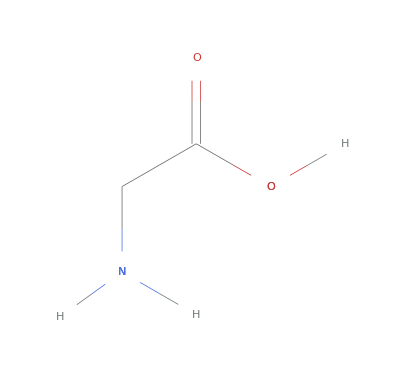
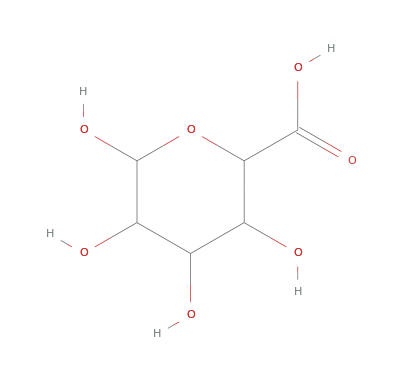
Glycine | Glucuronic Acid | Sulfate
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{"Glycine", "Glucuronic Acid", "Sulfate"}, {ChemicalData["Glycine"], ChemicalData["GlucuronicAcid"], -Graphics-}}, Frame -> All]
```

Once xenobiotic compounds have been converted to their hydrophilic moiety, they can be excreted, typically through renal (kidney) filtration into the bladder.

Most drugs undergo what is known as first-pass metabolism, undergoing metabolic changes in the liver.  It should be noted, however, that the metabolic process can occur at multiple locations in the body, including in the gut wall, as shown in this diagram from Nature Reviews | Drug Discovery.  Most of the drug, as indicated by the size of the black line, goes to the liver.  Some drug passes directly into the feces, where it is eliminated.  Once the drug gets through the liver, it is available for therapeutic use, and is defined as having bioavailability.

-Graphics-

Source : http://www.nature.com/nrd/journal/v2/n3/images/nrd1032-i2.gif

The graphic below provides a good snapshot of the processes involved in Phase I and Phase II metabolism.  A lipophilic compound can generally undergo oxidation or reduction/hydrolysis.  Hydrolysis (“water” + “lysis” (cutting)) is the breaking of a chemical bond by water.  Oxidized lipophiles are generally converted to electrophiles, or “electron-loving” compounds that interact with more positively-charged species.  These compounds then undergo glutathione conjugation to form the hydophilic R-SG compound.  Recall that the “R” notation represents some organic compound group, such as a methyl (-CH_3) or ethyl (-CH_2 CH_3) group.

Hydrolyzed/reduced lipophiles are converted to nucleophiles (“nucleus (positive)-loving”) substances, such as ROH, RSH, and RNH_2 compounds.  These can now be convered by Phase II reactions that include sulfation (addition of a sulfate group, SO_3 H), acetylation (acetyl group, CH_3 COO), or glucuronidation (C_6 H_10 O_7)

-Graphics-

Source:  https : // en.wikipedia.org/wiki/Drug_metabolism

The chart below (constructed from numerous sources) provides a brief overview of the most common type of reactions found in metabolism:

```mathematica
type={"Oxidation", "Reduction", "Hydrolysis", "Acylation", "Sulfate formation", "Amino Acid conjugation", "Glucuronic acid glutatione conjugation", "Mercapturic acid conjugation", "Methylation"};
phase = {"I", "I", "I", "II","II","II","II","II","II"};
descrip = {"Involves the initial insertion of a single oxygen atom \n onto the drug molecule,include hydroxylation, epoxidation, \n dealkylation, deamination and dehalogenation reactions.\n  The oxygen stays on the drug molecule with hydroxylation \n and epoxidation reactions and leaves the alkyl group as \n aldehyde with dealkylation reactions. ", "Reactions characterized by a gain in electrons. \n Compounds that are easily reduced are aldehydes, \n ketones, alkenes, nitro-compounds, azo-compounds and sulphoxides.",  "Defined as the addition of a water molecule to a compound.  \n Esters and amides are easily hydrolyzed.","Addition of a RC=O- group to a compound. This typically happens with \n aromatic amines, sulfonamides, hydrazines, hydrazides, and phenols.","Common reaction on phenols, alcohols, sulfonamides, and aromatic amines","Most common amino acids are glycine, glutamine, alanine, and arginine","Addition of a glucuronic acid to carboxylic acids, phenols, \n alcohols, amines, and thiols","A common conjugation reaction with halides, nitro groups, epoxides, \n sulfonates, and organophosphate groups","A detoxification reaction that produces a less polar and less excretable metabolite"};
Dataset[
Table[
<| 
"Reaction Type" -> type[[row]], 
"Phase" -> phase[[row]] , 
"Description" -> descrip[[row]]
|> ,
{row, 1, Length[type]}]
]
```

Reaction Type | Phase | Description
Oxidation | I | Involves the initial insertion of a single oxygen atom 
 onto the drug molecule,include hydroxylation, epoxidation, 
 dealkylation, deamination and dehalogenation reactions.
  The oxygen stays on the drug molecule with hydroxylation 
 and epoxidation reactions and leaves the alkyl group as 
 aldehyde with dealkylation reactions. 
Reduction | I | Reactions characterized by a gain in electrons. 
 Compounds that are easily reduced are aldehydes, 
 ketones, alkenes, nitro-compounds, azo-compounds and sulphoxides.
Hydrolysis | I | Defined as the addition of a water molecule to a compound.  
 Esters and amides are easily hydrolyzed.
Acylation | II | Addition of a RC=O- group to a compound. This typically happens with 
 aromatic amines, sulfonamides, hydrazines, hydrazides, and phenols.
Sulfate formation | II | Common reaction on phenols, alcohols, sulfonamides, and aromatic amines
Amino Acid conjugation | II | Most common amino acids are glycine, glutamine, alanine, and arginine
Glucuronic acid glutatione conjugation | II | Addition of a glucuronic acid to carboxylic acids, phenols, 
 alcohols, amines, and thiols
Mercapturic acid conjugation | II | A common conjugation reaction with halides, nitro groups, epoxides, 
 sulfonates, and organophosphate groups
Methylation | II | A detoxification reaction that produces a less polar and less excretable metabolite
2 levels | 9rows |  | Dataset[{__Association}]

## Section 2: Metabolic Processes, Reactions, and Enzymes

How do these reactions occur?  Most of them are catalyzed by a series of protein enzymes known as cytochrome P-450 enzymes.  These enzymes constitute what is knon as a superfamily of protein structures.  These include “sips” such as CYP3A4, CYP2D6, CYP2C9, CYP2C8, CYP2C19, CYP2E1, and CYP1A2 (note:  these are the metabolic enzymes found in software such as StarDrop).  The piechart below shows that the majority of commercially-viable drugs are metabolized by the CYP3A4 enzyme, with the rest metabolized by other CYP enzymes.  These variations in the CYP450 enzymes are commonly referred to as isoforms:

-Graphics-

Source :Matthew Segall, Jonathan Tyzack, Peter Hunt.  “Quantum Mechanical Models of P450 Metabolism to Guide Optimization of Metabolic Stability” (http://www.optibrium.com/news/presentations/QM_Models_of_P450_Metabolism.pdf)

The protein structure of a CYP is shown below.  This example is CYP3A4 (PDB: 1TQN), one of the more important metabolic enzymes.  This protein consists of 499 residues (amino acids), and has a secondary structure with 14 α-helices and six β-sheets.  This CYP is classified by the Enzyme Commission as EC1.14.13.97.  Most of the enzymes that are important in drug metabolism come from the major groups of 1, 2, and 3.

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=1TQN","PDB",ImageSize-> Medium]
```

-Graphics3D-

This protein is characterized by a major cofactor, in this case a protoporphyrin, a heme group containing a central iron (Fe), shown in the graphic below as a orange ball.

-Graphics-

CYP3A4 is an oxidoreductase, an enzyme that facilitates the transfer of an electron from one compound (the reductant) to another (the oxidant).  In the diagram below, you can follow the transfer of an electron from the Fe^(3+) moiety to Fe^(+2).  The overall reaction of interest is:  NADPH + H^+ + O_2 + Drug → NADP^+ + H_2O + Oxidized Drug

-Graphics-

Source:  S.P. Markey, Laboratory of Neurotoxicology, NIMH/NIH, November 2008.

Metabolic enzymes typically work in tandem to produce drug metabolites.  In the biochemical pathway diagram below, ibuprofen is shown in purple.  Ibuprofen is formulated as a racemic mixture of stereocompounds, the R- form and the S- form.  The primary CYPs, as can be seen from the diagram, are CYP2C9 and CYP2C19, although others, such as CYP2C8 and CYP3A4, also play a role with the R-form of the compound.

-Graphics-

Source:  https://www.pharmgkb.org/pathway/PA166041114

Both stereoisomers are metabolized primarily to hydroxy (-OH) metabolites.  This can be seen in the biochemical pathway graphic above, and in the metabolite diagram below, generated with the StarDrop P450 server.  Two metabolites are shown.  In the first metabolite, C4 (carbon 4, counting from the bottom up) is metabolized to remove a hydrogen and add a hydroxy group to the resulting space.  C4 is shown to be particular labile (44%), or unstable, so this is the first metabolite generated by one or more of the CYP enzymes.  Likewise, carbon-11 is moderately labile (34%), and it too replaces a hydrogen with a hydroxy group.  Hydroxy groups can also attach themselves to C1, C2, and C3 to form hydroxy-ibuprofen metabolites.

-Graphics-

Similarily, the nonsteroidal anti-inflammatory drug (NSAID) celecoxib undergoes metabolism to form the hydroxy product hydroxycelecoxib, and the parent and metabolite are shown below, both as a cartoon and as ball-and-stick figures:

-Graphics-

Another relatively easy example is the metabolism of codeine.  As shown in the figure below from PharmGKB.org, codeine can undergo metabolism by CYP3A4 to form norcodeine, which is also known as N-demethylcodeine, as a methyl group on a nitrogen atom is removed.  The nitrogen methyl group is 64% metabolized by CYP3A4.  Looking at the metabolite in the insert in the second panel, the methyl group attached to the nitrogen has been removed.  Likewise, the methyl group attached to the oxygen is 100% metabolized by CYP2D6.  The metabolite formed -- the O-demethylated form of codeine -- shows that the methyl group is removed from the oxygen, forming a metabolite that is more active than codeine -- morphine.  Both of these metabolites are more stable than codeine.  The demethylation process is a Phase I transformation.  Note that morphine now undergoes Phase II conjugation transformations to the glucuronide form of the compound. All of these processes occur in the liver cells.

Biochemical pathway 
(PharmGKB) | N-demethylation of 
codeine to norcodeine | O-demethylation of 
codeine to morphine
-Graphics- | -Graphics- | -Graphics-

The table below shows some examples of drugs that interact with the various isoforms of the CYP450 enzyme, either as substrates (activators) or as inhibitors.

-Graphics- | -Graphics-

Source:  http://medicine.iupui.edu/clinpharm/ddis/

The three-panel graphic below shows the CYP3A4 enzyme interacting with an inhibitor, in this case a carbamate, an organic molecule derived from carbamic acid (NH_2COOH).  On the far left, the enzyme is shown as a secondary structure.  The green wireframe is the active space (a “cavity”), where a ligand (or drug, in this case the carbamate) is likely to bind to the protein.  In the middle, the protein structure is removed, showing the interaction of the carbamate ligand with the binding site/active space of the protein. The next panel shows the ligand as a surface representation, signifying the electron density of the molecule.  Finally, on the far right, the ligand is shown in isolation.  Gray spheres are carbons, red spheres are oxygen, and blue spheres are nitrogens.  Green bonds represent rotatable bonds, while red bonds are rigid.

-Graphics- |  | -Graphics- | -Graphics-

Source:  PDB: 46DZ, graphics generated using the Molegro software

## Section 3: Controlling Metabolism in Drug Design

As a general rule, controlling metabolism means reducing or eliminating the amount of metabolism that a drug undergoes.  Having the drug stay at a concentration that results in a therapeutic effect, one that does not undergo clearance or one that has a longer halflife is a valuable property.  There are some situations, such as with a prodrug (discussed later in this chapter), in which rapid metabolism is a desired property, but generally speaking, delaying or reducing metabolism is a good thing.

There are no hard and fast rules for how one goes about reducing metabolism by one or more of the CYP450 enzymes.  The graphic below gives a rough idea of which groups are easily metabolized (harder substituents are at the bottom).

-Graphics-

Source : Matthew Segall, Jonathan Tyzack, Peter Hunt.  “Quantum Mechanical Models of P450 Metabolism to Guide Optimization of Metabolic Stability” (http://www.optibrium.com/news/presentations/QM_Models_of_P450_Metabolism.pdf)

The text below comes from Gareth Thomas’ Medicinal Chemistry: An Introduction:

Increasing the metabolic stability and hence the duration of action of a drug is usually achieved by replacing a reactive group with a less reactive one.  For example, N-dealkylation can be prevented by replacing an N-methyl group by an N-t-butyl group.  Reactive ester groups are replaced by less reactive amide groups.  Oxidation of aromatic rings may be reduced by introducting strong electron acceptor substituents such as chloro (-Cl), quaternary amine (-NR_3), carboxylic acid (-COOH), sulphonate (-SO_3R)and sulfonamide (-SO_2NHR) groups.  For example, replacement of the aryl methyl substituent of antidiabetic tolbutamide by chlorine yielded the antibiotic chorproamide, a compound with considerably longer half-life.

Tolbutamide | Chlorpropamide
Half-life (t_(1/2)): 7 hours  | Half-life (t_(1/2)): 35 hours 
 | 
Source:  Thomas, Gareth.  Medicinal Chemistry:  An Introduction, Second Edition, Wiley, 2007.

Another reference (Thompson, 2001), writes that “in general, metabolism can be reduced by incorporation of stable functions (blocking groups) at metabolically vulnerable sites.”  Continuing, the article states:

For the times when it is appropriate to enhance metabolic stability into the molecular design, the following strategies have been used:

Introducing an N-t-butyl group to prevent N-dealkylation.

Inactivating aromatic rings towards oxidation by substituting them with strongly electron withdrawing groups (e.g. CF_3, SO_2 NH_2, SO_3-).

Replacing a labile ester linkage with an amide group.

More generally, protecting the labile moiety by steric shielding.

Constraining the molecule in a conformation which is unfavorable to the metabolic pathway.

The phenolic function has consistently been shown to be rapidly glucuronidated.  Thus, avoidance of this moiety in a sterically unhindered position is advised in any compound intended for oral use.

Avoidance of other conjugation reactions as primary clearance pathways, would also be advised in the design stage in any drug destined for oral usage.

Sometimes the best strategy is to anticipate a likely route of metabolism and prepare the expected metabolite if it has adequate intrinsic activity.  For example, often N-oxides are just as active as the parent amine, but won’t undergo further N-oxidation.

The graphic below shows an example of how a drug can be modified to improve metabolism.  The goal in most cases is to reduce the amount of metabolism so that the drug stays concentrated in the blood for a longer period of time.  In this example, we have the drug salicylic acid on the left.  Salicylic acid is the precursor of aspirin, a non-steroidal anti-inflammatory drug (NSAID).  This lead drug comes from the bark of a willow tree, and is an excellent anti-inflammatory (pain) and anti-pyretic (fever).  Notice, however, that this drug is metabolized strongly by CYP3A4, especially at carbon-8, located next to a hydroxy-group (hydrogens are not shown).  This compound is labile at that carbon, meaning it is easily metabolised by that enzyme.  

In this example, the goal is simply to reduce the amount of metabolic activity by CYP3A4, to remove all of the “red” lability bars and to reduce the composite site lability (CSL) score, a unitless value that signifies the amount of metabolism for the entire molecule.  A CSL score of 1 indicates a very high degree of metabolism for the molecule, while a CSL score of 0 means absolutely no metabolism.  Salicylic acid has a very high score of 0.9271.  We want to decrease that value, in most cases.  Note that in decreasing the CSL score (by adding substituent groups), we also may change other parameters, including various ADME values and, more importantly, the pharmacological activity of the drug and its ability to effect a therapeutic response!  In this example, however, we are only interested in improving the metabolic response to the CYP3A4 enzyme.

One approach is acetylation, the addition of an acetyl group (CH_3 COO^-, the anion of acetic acid, or vinegar).  The hydroxy hydrogen is replaced by the acetyl group, forming acetylsalicylic acid, or ASA, the modern form of acid.  This drug has the same therapeutic value, without the side effects of stomach upset and formation of ulcers.  For our purposes here, however, note that addition of the acetyl group lowers the CSL value to 0.5429, a significant improvement in metabolic stability.  

We can also improve metabolic stability by adding bulky substituents, creating what is known as steric hindrance.  Bulky groups, like trifluromethyl (-CF_3), block access to the enzyme.  In the third card on the right, we have added a trifluromethyl group adjacent to the hydroxy group, forming trifluromethylsalicylic acid.  This addition reduces the CSL value significantly, to a value of 0.03361!  It is likely, however, that in doing so we have also reduced or elimnated any therapeutic effect, which is why you don’t see this compound on the market!

-Graphics-

Another example is shown starting with chlorazipine, an anti-psychotic drug used for the treatment of schizophrenia.  Starting on the left, one can see that chorazipine is metabolized strongly by CYP 3A4 at the methyl group attached to the first nitrogen.  Very little metabolism happens in the chloro-ring structures at the bottom part of the molecule.  In Analog 1, the methyl group has been removed, shifting the majority of the metabolism to the nitrogen and adjacent carbons.  The molecule is still labile, or metabolically unstable, with only a slight decrease in the CSL value.  An attempt is made to put two methyl groups on either side of the nitrogen, hoping to introduce some steric shielding to that nitrogen. This works, reducing the nitrogen metabolism by almost 50%, but also having the effect of shifting some the metabolism to the lower part of the molecule.  To increase the steric shielding, the methyl groups are replaced with very bulky trifluromethyl (CF_3) groups.  This has the effect of reducing the nitrogen metabolism by yet again another 50%, and now the molecule is only moderately labile.  What we don’t know, however, is the effect of shifting the metabolic interactions to the lower part of the molecule.  This may or may not have some impact on how the drug interacts with its eventual protein target.

Clorazipine | Analog 1 | Analog 2 | Analog 3
CSL:  0.9998 | CSL:  0.9961 | CSL:  0.9903 | CSL:  0.8961
-Graphics- | -Graphics- | -Graphics- | -Graphics-

It should be noted that the focus so far on applying drug design strategies to ensure metabolic stability have been to reduce metabolism.  There are, however, situations in which the goal is to increase the metabolism of a drug.  This is the case with prodrugs.  Prodrugs (as shown in the very first graphic in this chapter) are those drugs in which a therapeutically inactive drug is activated as a function of metabolism, and the resulting metabolite has therapeutic value.  Thomas (2000) describes some of the goals of creating a prodrug:

increase lipid or water solubility;

improve the taste of a drug to make it more patient compatible;

alleviate pain when the drug is administered parenterally by injection;

reduce toxicity;

increase chemical stability;

increase biological stability;

change the length of the time of duration of action;

deliver the drug to a specific site in the body.

One classic example is the drug valium (diazepam), a common (and probably over-prescribed) anti-anxiety medication.  The N-demethylated version of diazepam is known as nordazepam, but that compound is quickly metabolized and excreted before it makes its way through the liver.  Given as diazepam, however, the metabolised version is nordazepam, and giving the drug as diazepam increases the likelihood that a therapeutic amount of nordazepam will survive the journey through the liver.  The methyl group on one of the nitrogens (identified here as C1) is removed, and nordazepam (the metabolite) is shown in the insert window.  This metabolic process is catalyzed by the CYP34A enzyme.

-Graphics-

## References

Johnson, Virgina A.  “Introduction to Drug Metabolism”, http://slideplayer.com/slide/3581402/

Thomas, Gareth.  “Medicinal Chemistry:  An Introduction”.  John Wiley and Sons, Inc., New York, NY, 2000.

Markey, S.P.  “Drug Metabolism” (http://www.cc.nih.gov/training/training/principles/slides/PathDrugMet08-09oneslide.pdf), 2008.

Flockhart DA. Drug Interactions: Cytochrome P450 Drug Interaction Table. Indiana University School of Medicine (2007). “/clinpharm/ddis/clinical-table/” Accessed [date].

Shu, Yue-Zhong, Benjamin M. Johnson, and Tian J. Yang. “Role of Biotransformation Studies in Minimizing Metabolism-Related Liabilities in Drug Discovery.” The AAPS Journal 10.1 (2008): 178–192. PMC. Web. 22 Mar. 2016.

Matthew Segall, Jonathan Tyzack, Peter Hunt.  “Quantum Mechanical Models of P450 Metabolism to Guide Optimization of Metabolic Stability” (http://www.optibrium.com/news/presentations/QM_Models_of_P450_Metabolism.pdf)

Matthew Segall, Jonathan Tyzack, Peter Hunt.  “Predicting Regioselectivity and Lability of Cytochrome
P450 Metabolism using Quantum Mechanical Simulations” (http://www.opentox.net/dublin15/s4/SegallQMmodelsofP450metabolism.pdf)

Thompson, Thomas N. “Optimization of metabolic stability as a goal of modern drug design.” Medicinal research reviews 21.5 (2001): 412-449.